```mathematica
mu="1.2";
```

```mathematica
datFileLocalChernlocation="/data/topo_super/phase_diagram/";
```

```mathematica
band1filename=StringJoin["t0=1.0_t=1.0_mu=",ToString[mu],"_NGridpots=31_band1.csv"];
```

```mathematica
band2filename=StringJoin["t0=1.0_t=1.0_mu=",ToString[mu],"_NGridpots=31_band2.csv"];
```

```mathematica
(*Import the CSV file*)
band1data=Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,band1filename]];
band2data=Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,band2filename]];
```

```mathematica
NN =Dimensions[band1data][[1]]
```

14641

```mathematica
totalChernData = Table[{band1data[[nn]][[1]],band1data[[nn]][[2]],band1data[[nn]][[3]]+band2data[[nn]][[3]]},{nn,1,NN}];
```

```mathematica
(*Extract x,y,and value columns*)
values=Table[totalChernData[[ii]][[3]],{ii,1,NN}];
```

```mathematica
rainbowColor=Function[x,Which[x>2,Red,x<-2,Purple,True,ColorData["Rainbow"][Rescale[x,{-2,2}]]]];
```

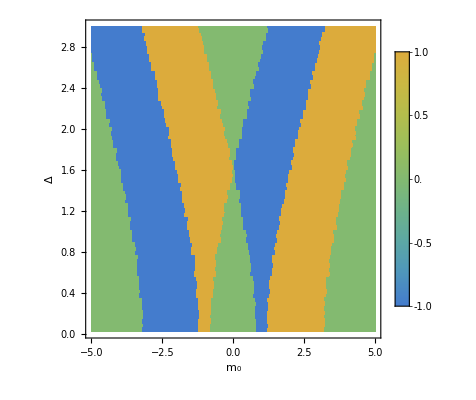

```mathematica
plt1=Show[ListDensityPlot[totalChernData,PlotRange->{All,{0.02,3},All},ColorFunction->rainbowColor,ColorFunctionScaling->False,PlotLegends->Automatic,InterpolationOrder->0],Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},RotateLabel->False,FrameLabel->{"m_0","Δ"},BaseStyle->20]
```

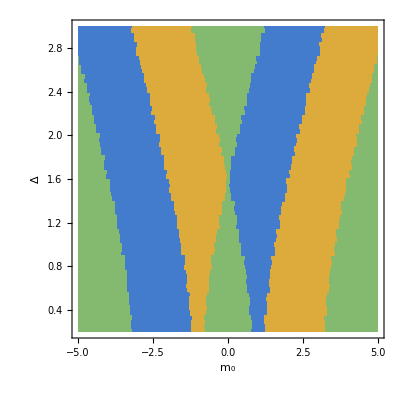

```mathematica
plt2=Show[ListDensityPlot[totalChernData,PlotRange->{All,{0.2,3},All},ColorFunction->rainbowColor,ColorFunctionScaling->False,PlotLegends->None,InterpolationOrder->0],Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},RotateLabel->False,FrameLabel->{"m_0","Δ"},BaseStyle->20]
```

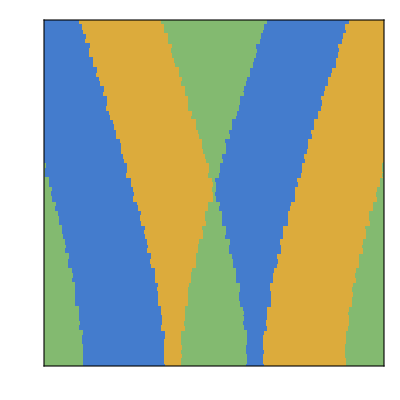

```mathematica
plt11=Show[ListDensityPlot[totalChernData,PlotRange->{All,All,All},ColorFunction->rainbowColor,ColorFunctionScaling->False,InterpolationOrder->0],Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},RotateLabel->False,FrameLabel->{None,None},BaseStyle->20,
FrameTicks-> {{{{3.0,""},{2.5,""},{2.0,""},{1.5,""},{1.0,""},{0.5,""}},None},{{{-4,""},{-3,""},{-2,""},{-1,""},{0,""},{1,""},{2,""},{3,""},{4,""}},None}},
PlotRange-> {{-3.99,3.99},{0.1,3.0}}]
```

```mathematica
(**Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,"t0=1.0_t=1.0_mu=",ToString[mu],"_NGridpots=31.pdf"],plt11];
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,"t0=1.0_t=1.0_mu=",ToString[mu],"_NGridpots=31_reduced.pdf"],Rasterize[plt11,ImageResolution->300]];
```